```mathematica
Quit[];
```

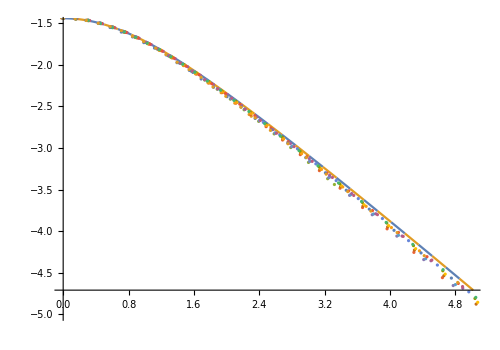

```mathematica
SetDirectory[NotebookDirectory[]];
sp0=Import["sp0.txt","Table"];
sp1=Import["sp1.txt","Table"];
n0 = (Length@sp0+1)/3;
n1 = (Length@sp1+1)/3;
cx=Join[sp0⟦1;;n0⟧,sp1⟦1;;n1⟧];
cy=Join[sp0⟦n0+1;;n0*2⟧,sp1⟦n1+1;;n1*2⟧];
h=Join[sp0⟦2 n0+1;;-1⟧,sp1⟦2n1+1;;-1⟧];
(*Length@data*)
Subscript[sx, i_][t_?NumberQ]:=cx⟦i,1⟧+cx⟦i,2⟧t+(cx⟦i,3⟧t^2+cx⟦i,4⟧t^3+cx⟦i,5⟧t^4+cx⟦i,6⟧t^5)
Subscript[sy, i_][t_?NumberQ]:=cy⟦i,1⟧+cy⟦i,2⟧t+(cy⟦i,3⟧t^2+cy⟦i,4⟧t^3+cy⟦i,5⟧t^4+cy⟦i,6⟧t^5)
{x[t_],y[t_]}=50(1+0.05Cos[8t-π]){Sin[t],Cos[t]};
res=Import["answer0.txt","Table"];
Table[{Subscript[sx, i][t],Subscript[sy, i][t]},{i,1,30,1}];
tt=ParametricPlot[{%⟦1;;Length@%;;2⟧,%⟦2;;Length@%;;2⟧},{t,0,1},AspectRatio->Automatic];
Show[(*,ParametricPlot[{x[t],y[t]},{t,0,π},PlotStyle->Red]*)
%
(*,ListPlot[Transpose[{cx⟦1;;-1,1⟧,cy⟦1;;-1,1⟧}]]*)
,Plot[c0 t^-0.5,{t,0,10}]
,ListPlot[bt,AspectRatio->Automatic]
,AspectRatio->Automatic,ImageSize->500,PlotRange->{{0,5},{-5,-1.5}}]
```

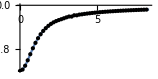

```mathematica
Clear[i,kv,kvt];dKv=0.00005;
kvt[t_]:=(x'[t]y''[t]-y'[t]x''[t])/(x'[t]^2+y'[t]^2)^1.5
θ=Table[ArcCos[Subscript[sy, i][0]/√((Subscript[sx, i][0])^2+ (Subscript[sy, i][0])^2)],{i,1,Length@cx}];//Quiet;
Subscript[kv, i_][t_]:=(Subscript[sx, i]'[t]Subscript[sy, i]''[t]-Subscript[sy, i]'[t]Subscript[sx, i]''[t])/((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)^1.5+Subscript[sy, i]'[t]/Subscript[sx, i][t]/√((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)
Flatten[Table[{Subscript[sx, i][#],Subscript[kv, i][#]}&/@Range[dKv,1+dKv,0.1],{i,1,50}],1];
ListPlot[%,PlotRange->All,Joined->True,Epilog->{Point@%⟦1;;-1;;10+1⟧},AspectRatio->0.5,PlotRange->{{0,5},{-2,-0}}]

(*ParametricPlot[{%⟦1;;Length@%;;2⟧,%⟦2;;Length@%;;2⟧},{t,0,1},AspectRatio->Automatic]*)
(*Table[{Subscript[sx, i][0.],Subscript[kv, i][0.]},{i,2,50 }];*)
(*Show[ListPlot[%,PlotRange->All,Joined->True],AspectRatio->0.5,PlotRange->All,Epilog->{Point@%}]*)
```

```mathematica
nrz = Normalize@Grad[(z-cc0 r),{r,z}]
b0 (r^2+z^2)^(1/4)LegendreP[1/2,z/(r r + z z)^(1/2)];
Grad[%,{r,z}].nrz;
%/.{cc0->c0,b0->1.759300000000000};

Series[%/.z->c0 r,{r,∞,2}]
```

{-cc0/(√(1+Abs[cc0]^2)),1/(√(1+Abs[cc0]^2))}

1.49291 √(1/r)+O[1/r]^(5/2)

```mathematica
Length@xc
```

599

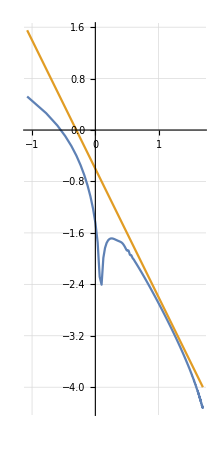

FittedModel[-0.685747-2.00417 t]

-0.603793

-0.91957

```mathematica
SetDirectory[NotebookDirectory[]];
xc = res⟦All,1⟧;
psin = res⟦All,2⟧;
res=Import["res.txt","Table"];
ListPlot[Log10@Abs@{
Transpose[{xc,psin+1.4929102712340343/√xc }]⟦2;;-1⟧,
Transpose[{xc,0.25 xc^-2 }]

}

,PlotRange->All,Joined->True,AspectRatio->Automatic,GridLines->Automatic]
LinearModelFit[Log10@Abs@Transpose[{xc,psin +1.4929102712340343/√xc}]⟦-500;;-300⟧,t,{t}]
Subscript[kv, 1][10^-10.]/2
res⟦1,2⟧/2
```

```mathematica
+1.760000000000000
```

FittedModel[0.140875-0.47498 t]

-0.604992

-0.91957

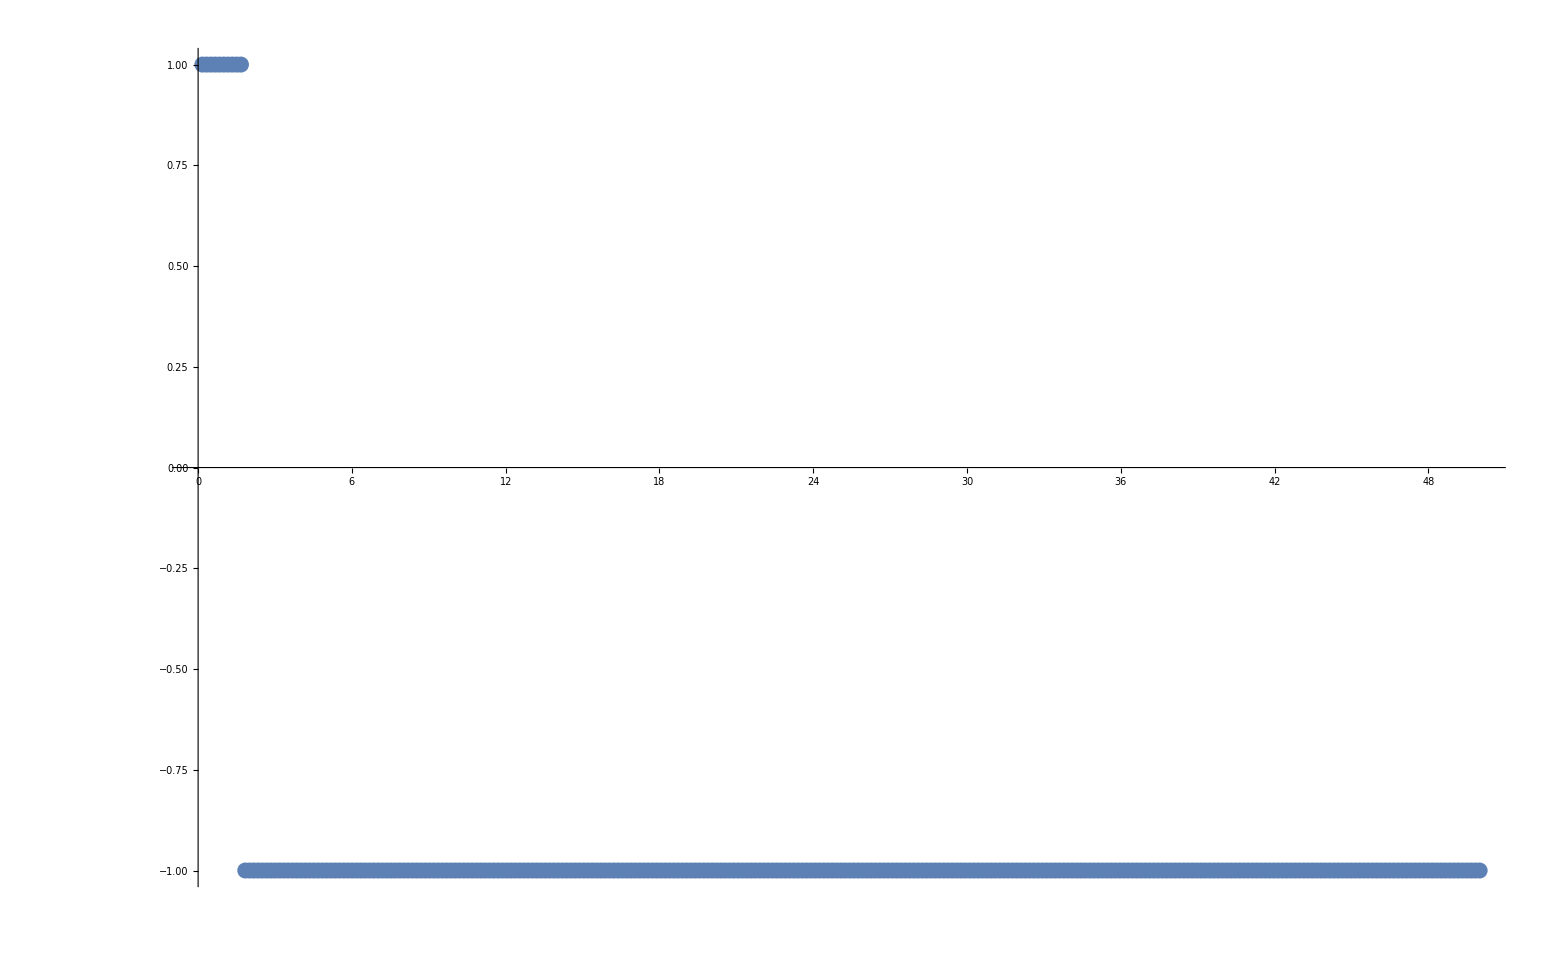

```mathematica
ListPlot[Transpose[{xx,Sign[yy-(-0.86043668612567826958329232241006895090205537938856512312860301418123537837128`49.759363080297355)xx-(
-0.87588 /√xx)]}]]
```

FittedModel[-1.86375-2.45828 t]

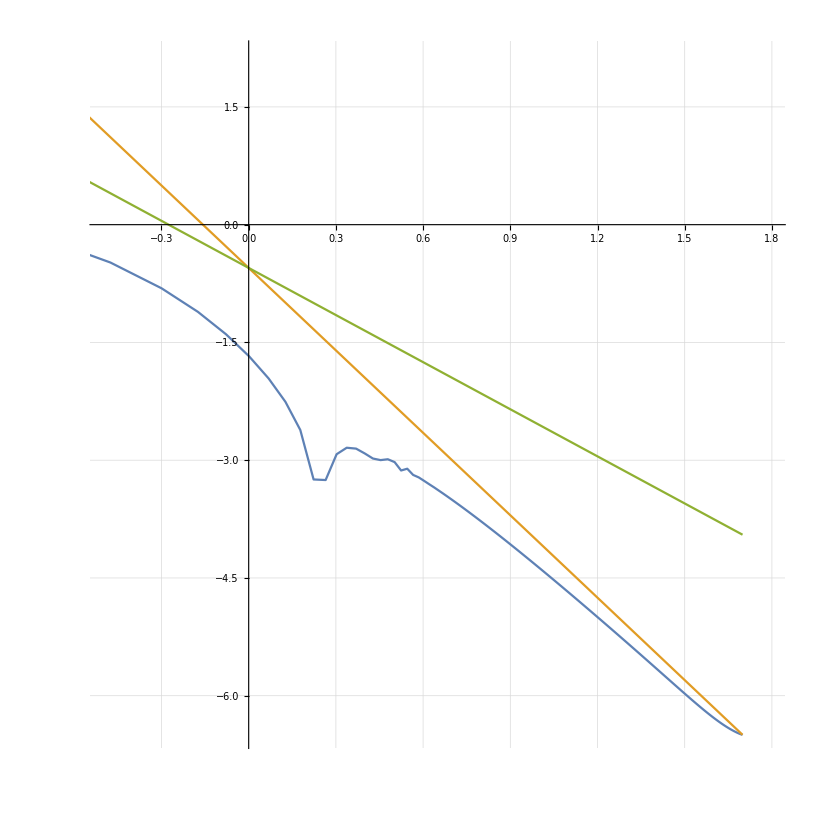

```mathematica
xx=cx⟦2;;n0,1⟧;
yy=cy⟦2;;n0,1⟧;
Log10@Abs@Transpose[{xx,yy-(-0.86043668612567826958329232241006895090205537938856512312860301418123537837128`49.759363080297355)xx-(-0.87588/√xx)}];
LinearModelFit[%⟦1;;60⟧,t,{t}]
ListPlot[{Log10@Abs@Transpose[{xx,yy-(-0.86043668612567826958329232241006895090205537938856512312860301418123537837128`49.759363080297355)xx-(
-0.87588/√xx)}],

Log10@Abs@Transpose[{xx,-0.28116 /xx^3.5}]⟦1;;-1⟧,
Log10@Abs@Transpose[{xx,-0.28116 /xx^2}]


},Joined->{True,True},GridLines->Automatic,AspectRatio->1,PlotRange->{{-0.5,1.8},Automatic}]
```

```mathematica
Log10@1.6
```

0.20412

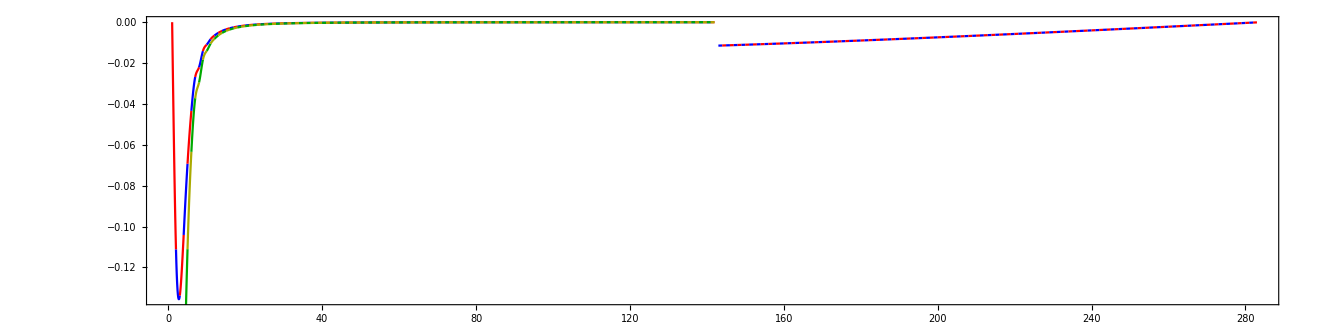

```mathematica
dv=2;
tx = Table[Flatten@{(#+i),Derivative[dv][Subscript[sx, i]][#]/h⟦i⟧^dv}&/@Range[0.0,1,0.1],{i,Join[Range[1,n0-1],Range[n0+1,n0+n1 -2]]}];
ty = Table[Flatten@{#+i,Derivative[dv][Subscript[sy, i]][#]/h⟦i⟧^dv}&/@Range[0.0,1,0.1],{i,Join[Range[1,n0-1],Range[n0+1,n0+n1 -2]]}];
(*ty = Table[{t+i,Derivative[dv][Subscript[sy, i]][t]/h⟦i⟧^dv},{i,1,Length@cx-1}];*)
Show[
ListPlot[tx,PlotStyle->{Red,Blue},Joined->True,PlotRange->All],
ListPlot[ty,PlotStyle->Darker@{Yellow,Green},Joined->True,PlotRange->All],
(*ParametricPlot[{ty⟦1⟧,ty⟦2⟧},{t,0,1}],*)
AspectRatio->0.25,Frame->True]
```

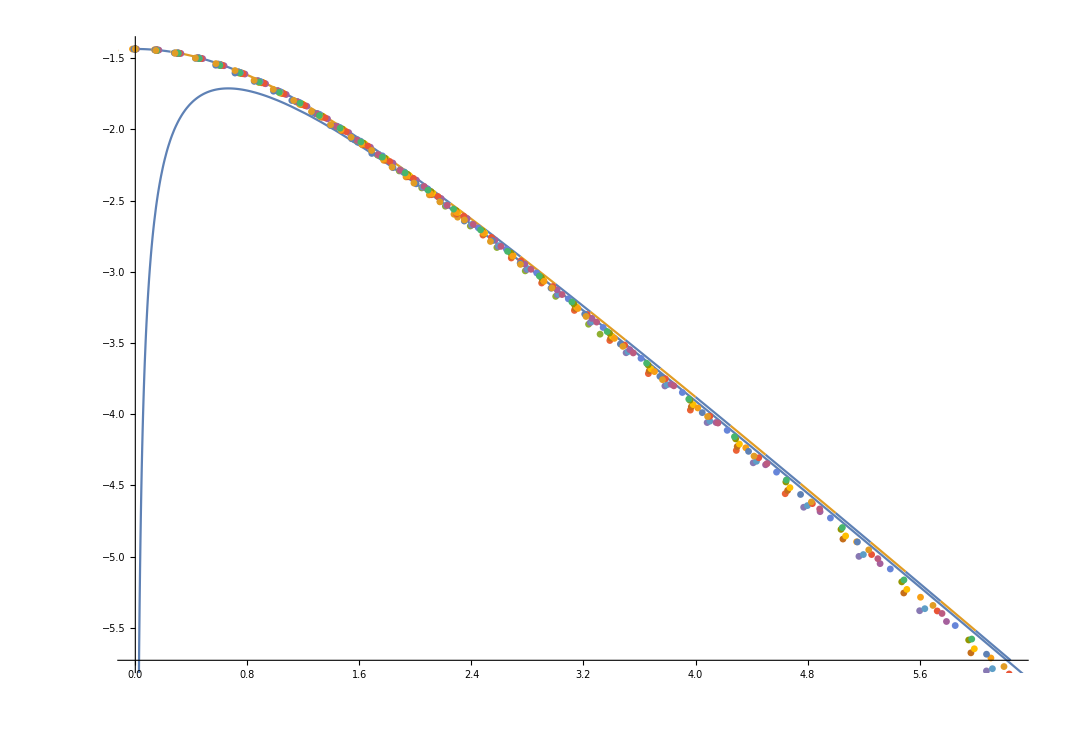

```mathematica
SetDirectory[NotebookDirectory[]];
bt=Import["C:\\Users\\czhou\\Documents\\LIS2T\\Preprint\\TaylorCone\\Resources\\DataFromBurtonPaper\\*.txt","Table","FieldSeparators"->","]⟦1;;-3⟧;
bt = DeleteDuplicatesBy[#,First]&/@bt;
origin=531.595;
ListPlot@bt;
shiftx = Interpolation[DeleteDuplicatesBy[#,First],InterpolationOrder->4]&/@bt;
findx=(t/.FindRoot[#'[t]==0,{t,497},WorkingPrecision->MachinePrecision])&/@shiftx;
Do[bt⟦i,All,1⟧=bt⟦i,All,1⟧ - findx⟦i⟧ ;
bt⟦i,All,2⟧=bt⟦i,All,2⟧ - origin;,{i,1,Length@bt}]
intbt=Interpolation[DeleteDuplicatesBy[#,First],InterpolationOrder->3][0]&/@bt;
Do[bt⟦i,All,1⟧=bt⟦i,All,1⟧ /Abs@intbt⟦i⟧;bt⟦i,All,2⟧=bt⟦i,All,2⟧ /Abs@intbt⟦i⟧;,{i,1,Length@bt}];
ListPlot[bt,AspectRatio->Automatic,Joined->True,PlotRange->{8{-1,1},8*0.86{-1,0}}];
scale= 1.4362982691445;
Do[bt⟦i,All,1⟧=bt⟦i,All,1⟧ *scale;bt⟦i,All,2⟧=bt⟦i,All,2⟧ *scale;,{i,1,Length@bt}]
Show[tt,Plot[c0 t+(-0.93) /√t,{t,0,10}],ListPlot[bt,AspectRatio->Automatic,PlotRange->{5{-1,1},5*0.86{-1,0}}]]
```

```mathematica
c0=-0.86043668612567826958329232241006895090205537938856512312860301418123537837128`49.759363080297355
```

-0.8604366861256782695832923224100689509020553793886